# Bset 0 playing with accelerometer data

```mathematica
SetDirectory[NotebookDirectory[]];
Import["../General.m"];
```

## 2b pushing phone on table

```mathematica
$2bRaw=Import["pushY.csv","Data"];
{"time","x","y","z","gforce"};
```

```mathematica
$2bHeader=$2bRaw[[1]]
$2bData=$2bRaw[[2;;Length[$2bRaw]-2]];
```

{time,x,y,z,gforce}

### Data came with strange white space, so clean it up!

```mathematica
cleanData[x_]:=Module[{},If[Length[x]≠4,{0,0,0,0},x]]
```

```mathematica
$2bCleanData=Map[cleanData,$2bData];
```

```mathematica
Dimensions[$2bData]
Dimensions[$2bCleanData]
```

{5290}

{5290,4}

### Let’s see what all three accelerations look like

```mathematica
Rasterize@ListLinePlot[{$2bCleanData[[All,{1,2}]],$2bCleanData[[All,{1,3}]],$2bCleanData[[All,{1,4}]]},PlotRange->All]
```

-Graphics-

### Let’s make a clear graph of just the push. We can see that the hand pushes the phone from .8 seconds to 1.07 seconds. After that, it decelerates at a constant rate

```mathematica
$2bPush=$2bCleanData[[All,{1,3}]][[150;;325]];
```

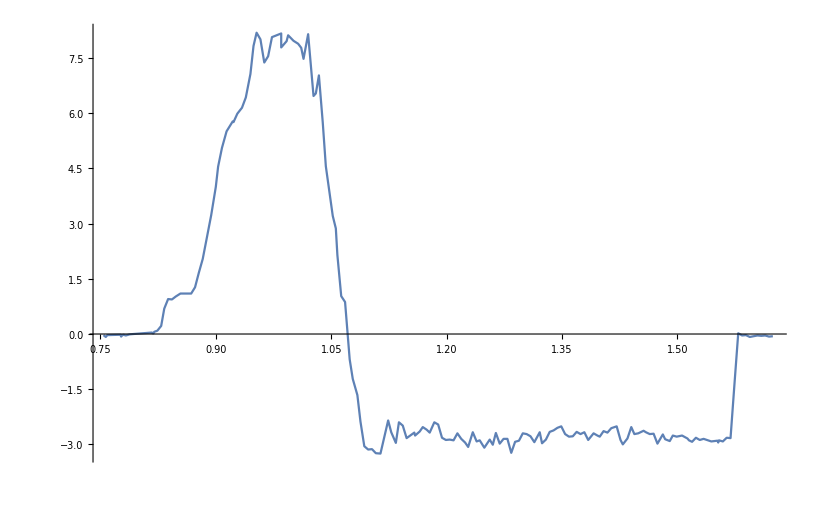

```mathematica
ListLinePlot[$2bPush,PlotRange->Full]
```

### Now, we using our data, we can calculate the velocity at any point in time using the previous velocity, the acceleration, and the time step.

### Position takes in a list containing tuples of times and accelerations. It returns a list of tuples containing times and positions. It should probably be separated into smaller functions at some point.

```mathematica
position[data_]:=Module[{n,timesteps,deltaVelocity,velocityAtIndex,lengthTimesteps,deltaDistances,timeAtIndex,distanceAtIndex},
n=Length[data];
timesteps=data[[2;;n,1]]-data[[1;;n-1,1]];
deltaVelocity=data[[2;;n,2]]*timesteps;
lengthTimesteps=Length[timesteps];
velocityAtIndex=Table[Total@deltaVelocity[[1;;i]],{i,lengthTimesteps}];
deltaDistances=velocityAtIndex*timesteps;
timeAtIndex=Table[Total@timesteps[[1;;i]],{i,lengthTimesteps}];
distanceAtIndex=Table[Total@deltaDistances[[1;;i]],{i,lengthTimesteps}];
Return[Transpose@{timeAtIndex,distanceAtIndex}]
]
```

### Plot of my position over time in a single direction. At the end, it looks like the phone has moved backwards. There could be a couple reasons for this. I think the phone was sensing accelerations in different directions as it slightly rotated. However, overall, the graph looks pretty good.

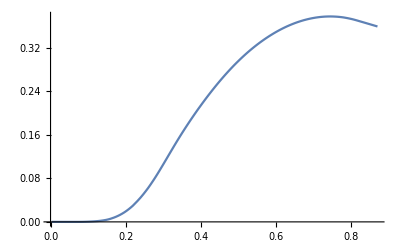

```mathematica
ListLinePlot[position[$2bPush]]
```

## 1a

```mathematica
$1aRaw=Import["walking.csv","Data"];
{"time","x","y","z","gforce"};
```

```mathematica
$1aHeader=$1aRaw[[1]]
$1aData=$1aRaw[[2;;Length[$1aRaw]-2]];
```

{time,x,y,z}

### Data came with strange white space, so clean it up!

```mathematica
$1aCleanData=Map[cleanData,$1aData];
```

```mathematica
Dimensions[$1aData]
Dimensions[$1aCleanData]
```

{2030,4}

{2030,4}

### Let’s see what all three accelerations look like

```mathematica
Grid[Transpose@{{"x","y","z"},Table[Rasterize@ListLinePlot[$1aCleanData[[All,{1,n}]],PlotRange->All],{n,{2,3,4}}]}]
```

x | -Graphics-
y | -Graphics-
z | -Graphics-

### Let’s make a clear graph of the walk. We can see that the walk ends around 10 seconds. After that, it was corrupted from doing other commands on the phone.

```mathematica
$1aWalk=$1aCleanData[[All,{1,2}]];
```

```mathematica
Rasterize@ListLinePlot[$1aWalk,PlotRange->Full,ImageSize->Large]
```

-Graphics-

### Given that I walked about 10 meters, I think my calculations might be a bit off somewhere.

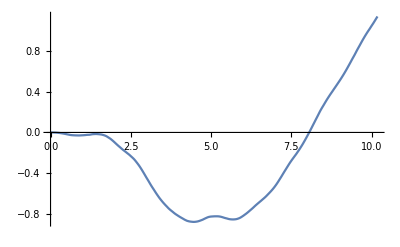

```mathematica
ListLinePlot@position[$1aWalk]
```

### This bset was fun and interesting. I’m still not sure whether or not my distance calculations were wrong because I wasn’t understanding my data correctly, or if my phone wasn’t giving out great data. It definitely seemed that my method of calculating position worked much better over a short period than a long period. I probably needed to use a high pass filter.

```mathematica
exportNotebookPDF[]
```

/home/nathan/olin/fall2016/qEAFall2016Homework/attitudeControl/bset0/bset0scratchbook.pdf